```mathematica
P= Flatten[Import["/home/lenny/Downloads/popdat.csv"]];
```

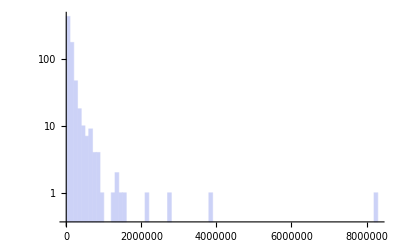

```mathematica
Histogram[Flatten[P],100,"LogCount"]
```

```mathematica
P=Sort[P,Greater];
```

```mathematica
Num = Table[i,{i,1,Length[P]}];
```

```mathematica
data = Transpose@{Num,P};
```

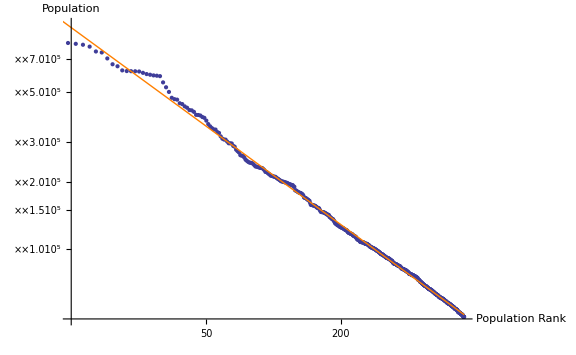

```mathematica
Show[ListLogLogPlot[data,AxesLabel->{"Population Rank","Population"},ImageSize->Large],LogLogPlot[Exp[15.6104]/x^0.725336,{x,1,716},PlotStyle->Orange]]
```

```mathematica
ldata = Log[data];
```

```mathematica
LinearModelFit[ldata,x,x]
```

FittedModel[15.6104-0.725336 x]

```mathematica
Pint = ConstantArray[0,715];
Pnorm = ConstantArray[0,715];
```

```mathematica
xm=10;α=0.01;
```

```mathematica
For[i=1,i<716,i++,Pint[[i]] =Total[P[[1;;i]]]/Total[P]]
```

```mathematica
For[i=1,i<716,i++,Pnorm[[i]] =P[[i]]/Total[P]]
```

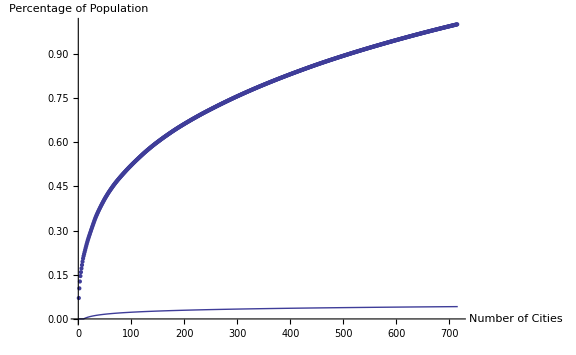

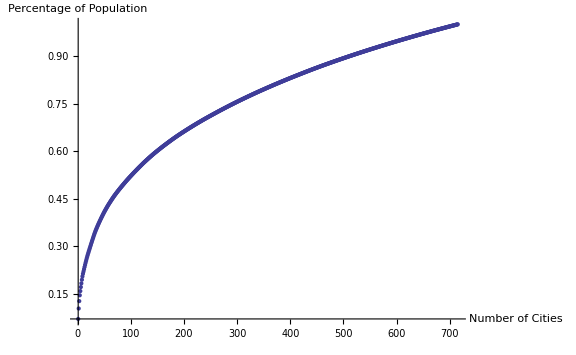

```mathematica
Show[Plot[If[x>xm,1-(xm/x)^α,0],{x,1,716},{PlotRange->All,AxesLabel->{"Number of Cities","Percentage of Population"},ImageSize->Large}],ListPlot[Pint,{PlotRange->All,AxesLabel->{"Number of Cities","Percentage of Population"},ImageSize->Large}]]
```

```mathematica
FKA = Table[0.06526009422282646/k^0.8125972580439725,{k,1,716}];
```

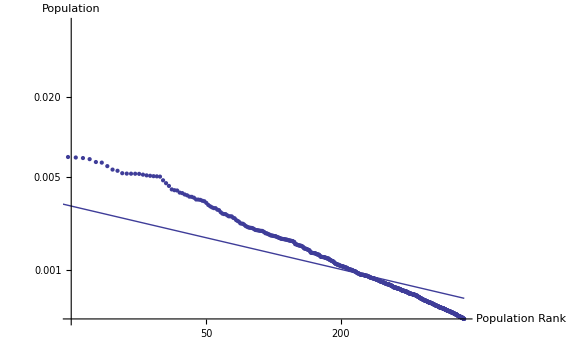

```mathematica
Show[ListLogLogPlot[{Pnorm},{PlotRange->All,AxesLabel->{"Population Rank","Population"},ImageSize->Large}],LogLogPlot[a/x^β/.{a->0.008212619742150672,β->0.3941362695462288},{x,1,716},PlotRange->All]]
```

```mathematica
0.06526009422282646/x^0.8125972580439725/.x->100
```

0.00154687

```mathematica
Pnorm[[100]]//N
```

0.00181451

```mathematica
Pnorm[[1]]
```

8244910/116204667

```mathematica
FindFit[Pnorm[[30;;]],a/x^β,{a,β},x]
```

{a→0.00821262,β→0.394136}

```mathematica
sampler[len_]:=Block[{y0,dist1,dist2,x0},y0=.5;
dist1[y_]:=RandomVariate[BinomialDistribution[16,y]];
dist2[x_]:=RandomVariate[BetaDistribution[x+2,16-x+4]];
Do[{x0=dist1[y0],y0=dist2[x0]},{1000}];
Table[{x0=dist1[y0],y0=dist2[x0]},{len}]];
```

```mathematica
data=sampler[715];
```

```mathematica
rand = Sort[1/RandomReal[1,715]^8,Greater];
```

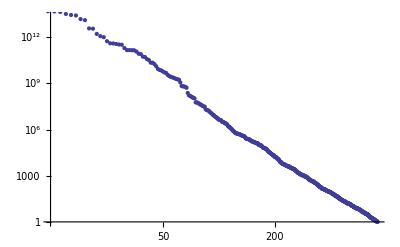

```mathematica
ListLogLogPlot[rand]
```

```mathematica
Q= Flatten[Import["/home/lenny/Dropbox/Current/initialvals.csv"]];
```

```mathematica
P1= Flatten[Import["/home/lenny/Dropbox/Current/vals15.csv"]];
```

```mathematica
P2= Flatten[Import["/home/lenny/Dropbox/Current/vals50.csv"]];
```

```mathematica
P3= Flatten[Import["/home/lenny/Dropbox/Current/vals75.csv"]];
```

```mathematica
P= Flatten[Import["/home/lenny/Dropbox/Current/finalvals.csv"]];
```

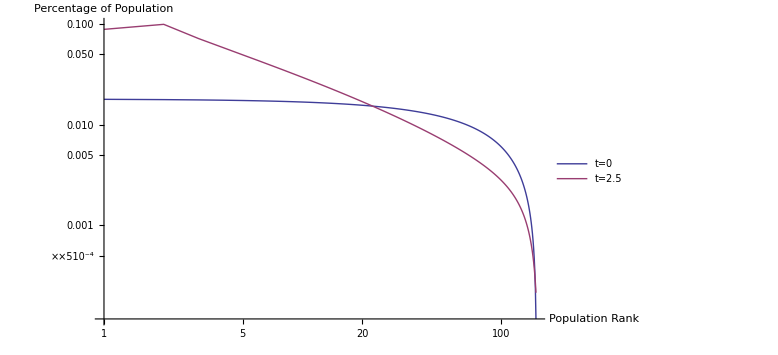

```mathematica
Show[ListLogLogPlot[{Q/50,P/50},{Joined->True,PlotRange->All,ImageSize->Large,AxesLabel->{"Population Rank","Percentage of Population"},PlotLegends->Placed[LineLegend[{"t=0","t=2.5","t=10"},LegendLayout->"Column"],{{0.25,0.45},{0.5,1}}]}]]
```

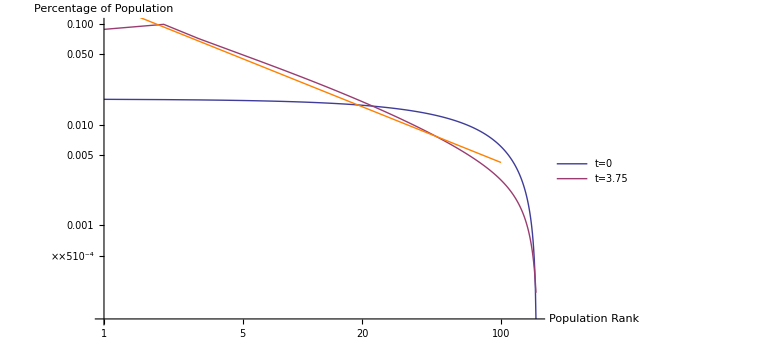

```mathematica
Show[ListLogLogPlot[{datum,data},{Joined->True,PlotRange->All,ImageSize->Large,AxesLabel->{"Population Rank","Percentage of Population"},PlotLegends->Placed[LineLegend[{"t=0","t=3.75"},LegendLayout->"Column"],{{0.25,0.45},{0.5,1}}]}],LogLogPlot[0.16/x^0.79,{x,1,100},PlotStyle->Orange]]
```

```mathematica
2500*0.001
```

2.5

```mathematica
Num = Table[i,{i,1,Length[P]}];
```

```mathematica
data = Transpose@{Num,P};
```

```mathematica
ldata = Log[data];
```

```mathematica
LinearModelFit[ldata,x,x]
```

FittedModel[3.57842868953231-1.497529329954877 x]

```mathematica
Num = Table[0.75*i,{i,1,Length[P]}];
```

```mathematica
data = Transpose@{Num,P};
```

```mathematica
datum[[;;,2]]=datum[[;;,2]]/50;
```

```mathematica
datum = Transpose@{Num,Q};
```

```mathematica
Total[dat[[;;,2]]]*0.75
```

1.02393

```mathematica
dat[[;;,2]]=dat[[;;,2]]/50
```

{0.159314178554491921,0.159125377710941436,0.0964582384492256928,0.0711627734384471911,0.0567865047130369494,0.0474968306750562963,0.0409021102234593403,0.0359820051881158687,0.032139076600576062,0.0290592645358604607,0.0265219570017492146,0.0243989657891730127,0.0225891577895423001,0.0210305192383942341,0.0196698044775395764,0.0184733890300147818,0.0174103962666461332,0.01646103714745768,0.0156060815151543864,0.0148331403017497077,0.0141295597908212978,0.0134872000556297889,0.0128973628742629276,0.0123544888216078341,0.0118523821311644673,0.0113871232439954495,0.0109541665584496828,0.0105506744339244007,0.0101732277277884475,0.00981972545184301771,0.00948754031984224588,0.00917508655844728516,0.00888030773412033958,0.00860198685013050635,0.00833848811178986682,0.00808886385409900321,0.00785179424189264008,0.00762653182411466402,0.00741199815844014065,0.00720759697483349226,0.00701243706375299869,0.00682603791314196573,0.00664765551887461559,0.00647689911628843373,0.0063131418589713395,0.00615606334885554829,0.00600513102089629935,0.00586008021030250514,0.00572045499255883216,0.00558603525366291542,0.0054564279464170673,0.00533144886784461591,0.00521075699477554499,0.00509419729256955445,0.00498147211899591769,0.00487245029670120455,0.00476687061877331009,0.00466462154592965472,0.00456547267806722668,0.00446932873558220367,0.00437598552840575028,0.0042853613116085304,0.00419727432373651177,0.00411165414154108566,0.00402833830044289798,0.00394726589025329477,0.00386829113319057116,0.00379136114521192336,0.00371634464715693613,0.00364319555191490896,0.0035717952343046272,0.00350210338269779153,0.00343401246276385519,0.00336748708543409159,0.00330242947618384797,0.00323880845307183252,0.00317653486276284869,0.00311558112779886265,0.00305586573783450999,0.00299736421026234878,0.00294000183395194847,0.00288375678860652407,0.00282856043174003036,0.00277439323704077867,0.00272119199588692462,0.00266893916137352416,0.00261757640539381331,0.0025670878910747591,0.00251741968701286012,0.00246855743519530907,0.00242045117675462274,0.00237308783381446176,0.00232642104726068139,0.00228043884833244698,0.00223509814934991696,0.00219038794342821114,0.00214626812464922073,0.00210272852129985477,0.00205973175329467517,0.00201726837523407559,0.00197530350653760511,0.00193382833487805578,0.00189281027894760451,0.00185224108002250837,0.0018120902789586163,0.00177235010341443067,0.00173299205990243788,0.00169400880623452599,0.001655373676534517,0.00161707971250237587,0.00157910195447334645,0.00154143379089591859,0.00150405186202165697,0.00146694987435697338,0.00143010597557405361,0.00139351416945389328,0.00135715403128806866,0.00132101984882681045,0.00128509255693982277,0.00124936672118178896,0.00121382457892871401,0.0011784609742508366,0.0011432594002576707,0.001108214986911637,0.00107331244600978218,0.00103854720727455788,0.00100390517337654833,0.000969382094000357242,0.000934965043670483581,0.000900650118410927514,0.000866425553974350254,0.000832287825094398387,0.000798226326136194791,0.000764237948678891249,0.00073031325070621142,0.000696449584247667564,0.000662638683118953187,0.000628878408482359125,0.000595161688942198175,0.000561486948040193362,0.000527848334332010685,0.000494244890886380989,0.000460672016944136953,0.000427129435307777722,0.000393613831450592283,0.000360125670126961867,0.000326662962498902587,0.000293226978222678493,0.000259817096440144203,0.000226435453858695145}

```mathematica
datum = Transpose@{Num,Q};
```

```mathematica
Num
```

{0.75,1.5,2.25,3.,3.75,4.5,5.25,6.,6.75,7.5,8.25,9.,9.75,10.5,11.25,12.,12.75,13.5,14.25,15.,15.75,16.5,17.25,18.,18.75,19.5,20.25,21.,21.75,22.5,23.25,24.,24.75,25.5,26.25,27.,27.75,28.5,29.25,30.,30.75,31.5,32.25,33.,33.75,34.5,35.25,36.,36.75,37.5,38.25,39.,39.75,40.5,41.25,42.,42.75,43.5,44.25,45.,45.75,46.5,47.25,48.,48.75,49.5,50.25,51.,51.75,52.5,53.25,54.,54.75,55.5,56.25,57.,57.75,58.5,59.25,60.,60.75,61.5,62.25,63.,63.75,64.5,65.25,66.,66.75,67.5,68.25,69.,69.75,70.5,71.25,72.,72.75,73.5,74.25,75.,75.75,76.5,77.25,78.,78.75,79.5,80.25,81.,81.75,82.5,83.25,84.,84.75,85.5,86.25,87.,87.75,88.5,89.25,90.,90.75,91.5,92.25,93.,93.75,94.5,95.25,96.,96.75,97.5,98.25,99.,99.75,100.5,101.25,102.,102.75,103.5,104.25,105.,105.75,106.5,107.25,108.,108.75,109.5,110.25,111.,111.75,112.5}

```mathematica
dat
```

{{0.75,3.17983516486365936},{1.5,3.17202800853544442},{2.25,2.70502954884484659},{3.,2.39810205480782468},{3.75,2.1629828549342629},{4.5,1.97808634462916833},{5.25,1.82540562612821811},{6.,1.6975367828578054},{6.75,1.58756346908498491},{7.5,1.49217736056228501},{8.25,1.40800603814500458},{9.,1.33331899042135804},{9.75,1.26622909507861947},{10.5,1.205732503291711},{11.25,1.15067200280750415},{12.,1.10042092332425856},{12.75,1.05422134720875471},{13.5,1.01165997118591156},{14.25,0.97221501167290092},{15.,0.935601981570405972},{15.75,0.9014473029645097},{16.5,0.869548332785093803},{17.25,0.839628995342244},{18.,0.811540834098636643},{18.75,0.785074419743751584},{19.5,0.760118410457007343},{20.25,0.736510401504719026},{21.,0.714165207690287684},{21.75,0.692954505151994971},{22.5,0.672811995641727556},{23.25,0.653634628444599408},{24.,0.635370031524946533},{24.75,0.617934272002881979},{25.5,0.601285435245336286},{26.25,0.585354303731101422},{27.,0.570106942316002341},{27.75,0.555485635398189737},{28.5,0.54146262359671149},{29.25,0.527989305129696773},{30.,0.515042761243266534},{30.75,0.502581700559970868},{31.5,0.490587041750477459},{32.25,0.479023422232404905},{33.,0.467874834067292356},{33.75,0.457110771178567243},{34.5,0.446717709980670064},{35.25,0.436669158823361547},{36.,0.426953619272599894},{36.75,0.417547945674111187},{37.5,0.408442303104823878},{38.25,0.399616356076640422},{39.,0.391061645701076377},{39.75,0.382760213226038148},{40.5,0.374704745303882758},{41.25,0.36687930638738725},{42.,0.35927754238998888},{42.75,0.351885250378867309},{43.5,0.344696883868703674},{44.25,0.337699731972830319},{45.,0.330888931484828786},{45.75,0.32425306307940549},{46.5,0.317787844264028507},{47.25,0.311482979156554318},{48.,0.305334680857191065},{48.75,0.299333635131995401},{49.5,0.293476479634992349},{50.25,0.287754761538190018},{51.,0.282165483452842147},{51.75,0.276700951473236367},{52.5,0.27135848292572301},{53.25,0.26613105506306145},{54.,0.261016257376736671},{54.75,0.256007662784336176},{55.5,0.251103096753034938},{56.25,0.246296662654737042},{57.,0.241586391030448627},{57.75,0.236966859157955151},{58.5,0.232436276168732942},{59.25,0.227989644030452382},{60.,0.223625327692770742},{60.75,0.219338710833569484},{61.5,0.21512829458106833},{62.25,0.210989806672148589},{63.,0.206921867431849316},{63.75,0.202920515578094429},{64.5,0.198984475917772463},{65.25,0.195110069014406445},{66.,0.191296111385441919},{66.75,0.187539179718374},{67.5,0.183838171146070734},{68.25,0.180189895727588478},{69.,0.176593321570411299},{69.75,0.17304547194702552},{70.5,0.169545377568993211},{71.25,0.166090257041445394},{72.,0.162679196427106182},{72.75,0.159309593791908233},{73.5,0.155980584288068991},{74.25,0.152689731351824759},{75.,0.149436213850189292},{75.75,0.146217748087424909},{76.5,0.143033552072030445},{77.25,0.139881483898367187},{78.,0.136760796874789009},{78.75,0.133669481093246334},{79.5,0.130606821995842143},{80.25,0.127570933047419205},{81.,0.124561129288673439},{81.75,0.121575640001153396},{82.5,0.118613807885265724},{83.25,0.115673971468014031},{84.,0.112755499740652562},{84.75,0.109856834819263213},{85.5,0.106977371167938165},{86.25,0.104115649691849166},{87.,0.101271090047445569},{87.75,0.098442327936744789},{88.5,0.0956288084569118929},{89.25,0.0928292588819174397},{90.,0.090043150521563961},{90.75,0.0872692997305928864},{91.5,0.0845072053237966442},{92.25,0.0817557709508615338},{93.,0.0790145247419989233},{93.75,0.0762824565368388496},{94.5,0.0735591261064479918},{95.25,0.0708436090340042318},{96.,0.0681354995664359281},{96.75,0.0654339592211816978},{97.5,0.0627386200559640339},{98.25,0.0600487303278372797},{99.,0.0573639637242853995},{99.75,0.0546836566367181129},{100.5,0.0520075286610016119},{101.25,0.0493350062770201506},{102.,0.0466658596919862015},{102.75,0.0439996079509152246},{103.5,0.0413360769508394135},{104.25,0.0386748812552158081},{105.,0.0360159078398262292},{105.75,0.0333588701593291181},{106.5,0.0307037218836692764},{107.25,0.0280502790801008123},{108.,0.0253985678491543618},{108.75,0.0227485108540756431},{109.5,0.020100212354150146},{110.25,0.0174537057495584951},{111.,0.0148091790234207675},{111.75,0.0121667804874272933},{112.5,0.00952678706909252174}}